```mathematica
ClearAll["Global`*"];
(* W wodzie rozchodzi się fala akustyczna o częstotliwości f i natężeniu I. Prędkość fazowa wynosi v=1500 m/s ^-1. Sporządzić wykresy zależności
amplitudy, maksymalnej prędkości i maksymalnego przyspieszenia
drgań cząsteczek ośrodka od f dla f zmieniającego się od 10 kHz do
20 kHz w dwóch przypadkach:
I=1 W/m.b2                I=5 W/m.b2. *)
```

```mathematica
ω=2×π×f;
```

```mathematica
r1=Solve[J==1/2×ρ×vf×A^2×ω^2,A]
```

{{A→-(√J)/(√2 f π √vf √ρ)},{A→(√J)/(√2 f π √vf √ρ)}}

```mathematica
A[J_,f_]=A/.r1[[2,1]]
```

(√J)/(√2 f π √vf √ρ)

```mathematica
x=A×Sin[ω×t+ϕ];
vmax[J_,f_]=D[x, t]/.A->A[J,f]/.Cos[ϕ+ω×t]->1
amax[J_,f_]=D[x, t,t]/.A->A[J,f]/.Sin[ϕ+ω×t]->1
```

(√2 √J)/(√vf √ρ)

-(2 √2 f √J π)/(√vf √ρ)

```mathematica
vf=1500;                   (* m/s *)
```

```mathematica
ρ=10^3;                      (* kg/m^3 *)
```

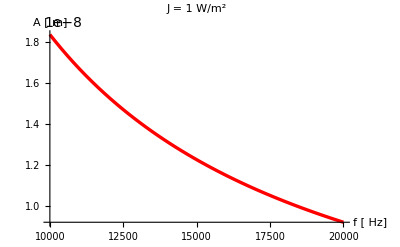

```mathematica
Plot[A[1,f],{f,10×10^3,20×10^3},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},PlotLabel->StyleForm["J = 1 W/m^2",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],
AxesLabel->{"f [ Hz]","A [ m]"}]
```

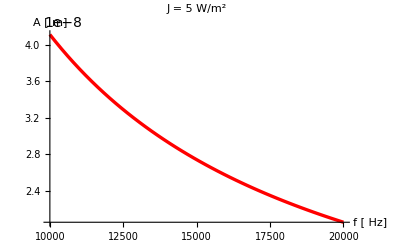

```mathematica
Plot[A[5,f],{f,10×10^3,20×10^3},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},PlotLabel->StyleForm["J =  5 W/m^2",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],
AxesLabel->{"f [ Hz]","A [ m]"}]
```

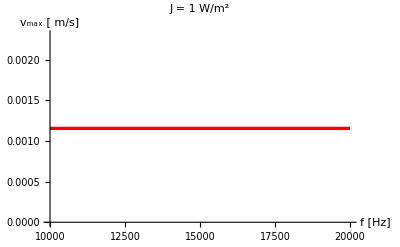

```mathematica
Plot[vmax[1,f],{f,10×10^3,20×10^3},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},PlotLabel->StyleForm["J = 1 W/m^2",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],
AxesLabel->{"f [Hz]","v_max [ m/s]"}]
```

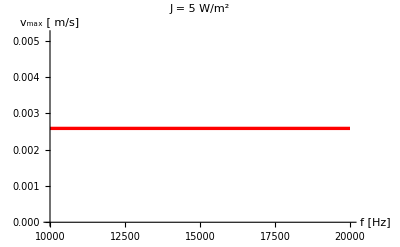

```mathematica
Plot[vmax[5,f],{f,10×10^3,20×10^3},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},PlotLabel->StyleForm["J = 5 W/m^2",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],
AxesLabel->{"f [Hz]","v_max [ m/s]"}]
```

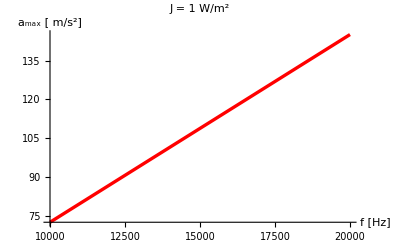

```mathematica
Plot[Abs[amax[1,f]],{f,10×10^3,20×10^3},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},PlotLabel->StyleForm["J = 1 W/m^2",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],
AxesLabel->{"f [Hz]","a_max [ m/s^2]"}]
```

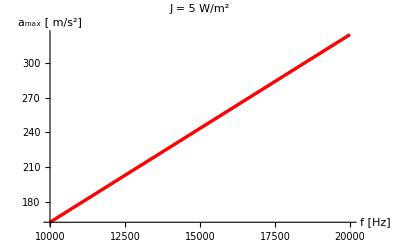

```mathematica
Plot[Abs[amax[5,f]],{f,10×10^3,20×10^3},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},PlotLabel->StyleForm["J = 5 W/m^2",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],
AxesLabel->{"f [Hz]","a_max [ m/s^2]"}]
```